```mathematica
SetDirectory[NotebookDirectory[]];
fRand[aXorY_,aRho_]:=RandomVariate[NormalDistribution[5+aRho(aXorY-5),1-aRho^2],{1}][[1]]
fStep[aXInd_Integer,aX_,aY_,aRho_]:=If[aXInd==1,{0,fRand[aY,aRho],aY},{1,aX,fRand[aX,aRho]}]
fGibbs[aNumIterations_Integer,aXStart_,aYStart_,aRho_]:=NestList[fStep[#[[1]],#[[2]],#[[3]],aRho]&,{1,aXStart,aYStart},aNumIterations][[All,2;;3]]
fSelectNewSite[aCurrentLocation_,aSigma_]:=Mod[aCurrentLocation+RandomVariate[MultinormalDistribution[{0,0},{{aSigma,0},{0,aSigma}}],1][[1]],10]
fRand[x_,y_,aRho_]:=PDF[MultinormalDistribution[{5,5},{{1,aRho},{aRho,1}}],{x,y}]
fRand1[x_,y_]:=fRand[x,y,0.5]
fRand2[x_,y_]:=fRand[x,y,0.99]
fStepMetropolis[aCurrentLocation_,aSigma_,fRand_]:=Module[{aNewLocation=fSelectNewSite[aCurrentLocation,aSigma],aCurrentB=fRand@@aCurrentLocation,aNewB,r,p=RandomReal[]},aNewB=fRand@@aNewLocation; r=aNewB/aCurrentB; If[r>p,aNewLocation,aCurrentLocation]]
```

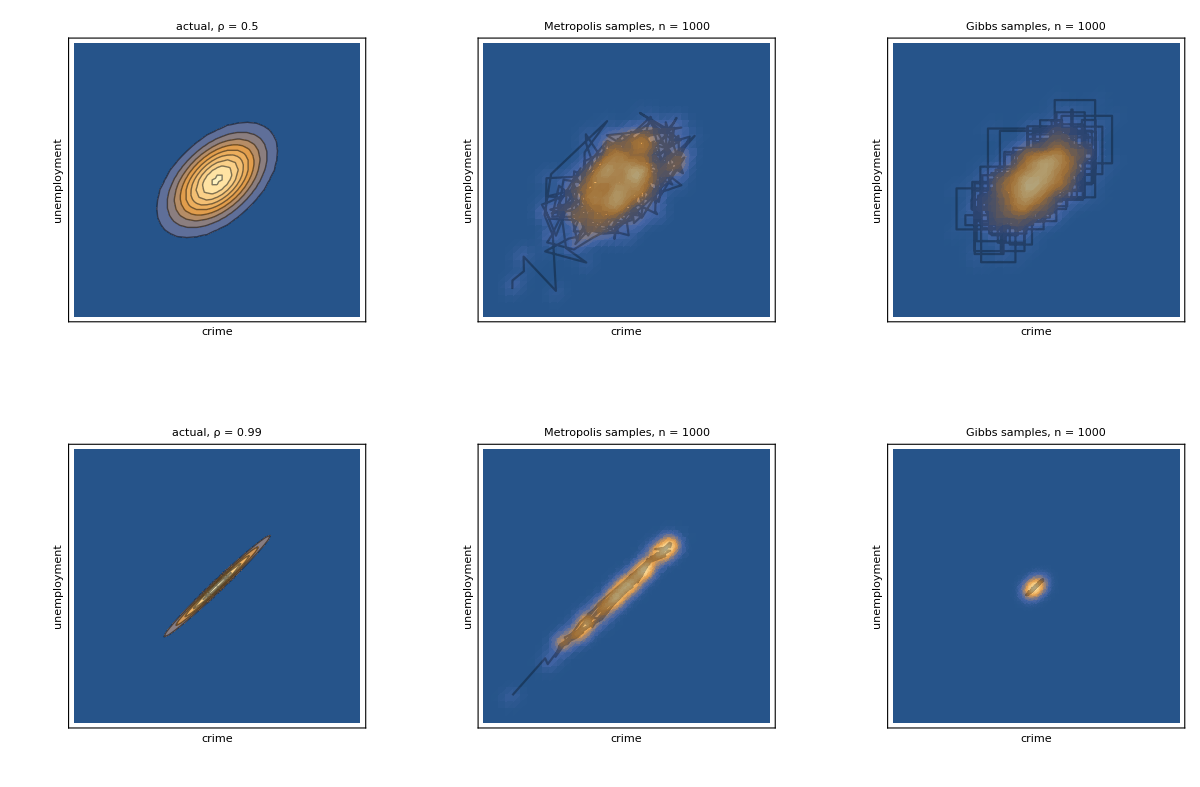

```mathematica
n1=1000;
lNumSamplesGibbs=fGibbs[n1,5,5,0.5];
lNumSamplesMetropolis=NestList[fStepMetropolis[#,1,fRand1]&,{1,1},n1];
lNumSamplesGibbs2=fGibbs[n1,5,5,0.99];
lNumSamplesMetropolis2=NestList[fStepMetropolis[#,1,fRand2]&,{1,1},n1];
aPlotRange={{0,10},{0,10}};
bPlotRange={{0,10},{0,10},Full};
aKernelWidth=0.2;
g1=ContourPlot[fRand[x,y,0.5],{x,0,10},{y,0,10},PlotRange->bPlotRange, PerformanceGoal->"Quality",FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},PlotLabel->"actual, ρ = 0.5"];
g2=Show[SmoothDensityHistogram[lNumSamplesGibbs,aKernelWidth,PlotRange->aPlotRange,FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Gibbs samples, n = 1000"],ListLinePlot[lNumSamplesGibbs,PlotStyle->Opacity[0.3,Black]]];
g3=Show[SmoothDensityHistogram[lNumSamplesMetropolis,aKernelWidth,PlotRange->aPlotRange,FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Metropolis samples, n = 1000"],ListLinePlot[lNumSamplesMetropolis,PlotStyle->Opacity[0.3,Black]]];
g4=ContourPlot[fRand[x,y,0.99],{x,0,10},{y,0,10},PlotRange->bPlotRange, PerformanceGoal->"Quality",FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},PlotLabel->"actual, ρ = 0.99"];
g5=Show[SmoothDensityHistogram[lNumSamplesGibbs2,aKernelWidth,PlotRange->aPlotRange,FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Gibbs samples, n = 1000"],ListLinePlot[lNumSamplesGibbs2,PlotStyle->Opacity[0.3,Black]]];
g6=Show[SmoothDensityHistogram[lNumSamplesMetropolis2,aKernelWidth,PlotRange->aPlotRange,FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Metropolis samples, n = 1000"],ListLinePlot[lNumSamplesMetropolis2,PlotStyle->Opacity[0.3,Black]]];
gFinal=Show[GraphicsGrid[{{g1,g3,g2},{g4,g6,g5}}],ImageSize->1200]
```

```mathematica
Export["Gibbs_correlationProblemCrime.png",gFinal]
```

Gibbs_correlationProblemCrime.png